```mathematica
SetDirectory[NotebookDirectory[]]
<<"/home/juanathan/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Plane_Interface.wls"

fs = 9;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
graphsOpts:= {Mesh-> Full,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> ColorData[3]}
SetOptions[ListLinePlot,graphsOpts];
```

/home/juanathan/Documentos/Wolfram Mathematica/Wolfram_scripts

## Fresnel

### Amplitude Coefficients

{4,19}

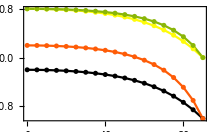

```mathematica
(*As function of the incident angle*)
ang = Range[0.,90.,5.]*Pi/180.;
refInd = {1,1.5};
functions ={FresnelReflectionS,FresnelReflectionP,FresnelTransmissionS,FresnelTransmissionP};

data =#[ang,refInd]&/@ functions;
Dimensions[data]
ListLinePlot[data,Mesh->All, PlotLegends->functions,DataRange->{0,90}]
```

{4,16}

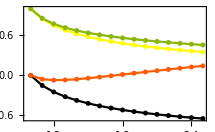

```mathematica
(*As function of the refractive index*)
ang = 60*Pi/180.;
refInd = Transpose[{1., #}&/@ Range[1,2.5,.1]];
functions ={FresnelReflectionS,FresnelReflectionP,FresnelTransmissionS,FresnelTransmissionP};

data =#[ang,refInd]&/@ functions;
Dimensions[data]
ListLinePlot[data,Mesh->All, PlotLegends->functions, DataRange->{1,2.5}]
```

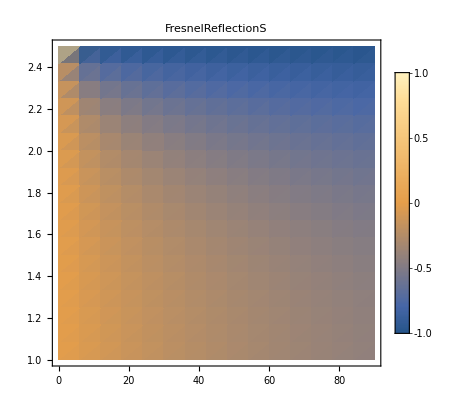
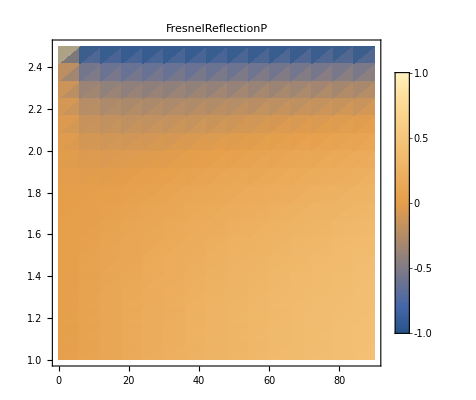
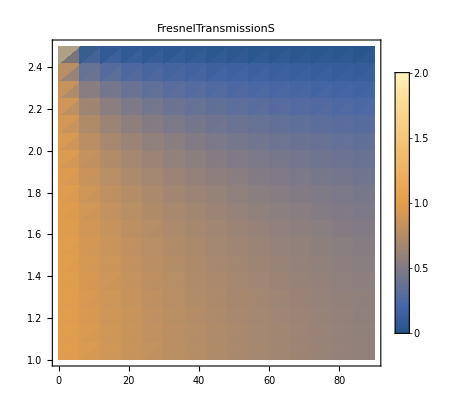
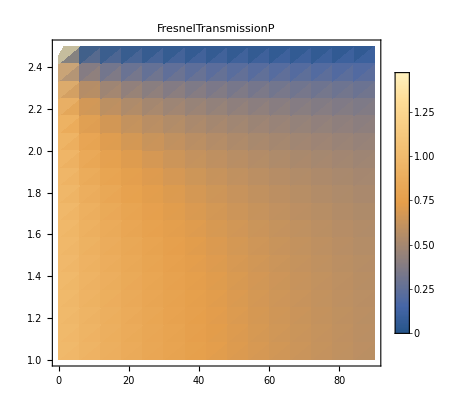

```mathematica
(*As function of the angle of incidence and the refractive index*)
ang = Range[0.,90.,5.]*Pi/180.;
refInd = Transpose[{1., #}&/@ Range[1,2.5,.1]];
functions ={FresnelReflectionS,FresnelReflectionP,FresnelTransmissionS,FresnelTransmissionP};

Table[data = f[ang,refInd];
ListDensityPlot[data, PlotLegends->Automatic, PlotLabel->f, DataRange->{{0,90},{1,2.5}}],{f,functions}]
```

### Reflectance and Transmittance

{FresnelReflectionS,FresnelReflectionP,FresnelTransmissionS,FresnelTransmissionP}

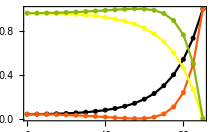

```mathematica
(*As function of the incident angle*)
ang = Range[0.,90.,5.]*Pi/180.;
refInd = {1,1.5};
functions ={FresnelReflectionS,FresnelReflectionP,FresnelTransmissionS,FresnelTransmissionP}

data =#[ang,refInd]&/@ functions;
imp = FresnelImpedance[ang, refInd];
trans = norm2[#]*imp & ;
ListLinePlot[
	Join[norm2[data[[;;2]]], trans/@ data[[3;;4]]],
		Mesh->All,PlotRange->All, PlotLegends->functions,DataRange->{0,90}]
```

{FresnelReflectionS,FresnelReflectionP,FresnelTransmissionS,FresnelTransmissionP}

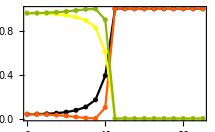

```mathematica
(*As function of the incident angle*)
ang = Range[0.,90.,5.]*Pi/180.;
refInd = {1.5,1.};
functions ={FresnelReflectionS,FresnelReflectionP,FresnelTransmissionS,FresnelTransmissionP}

data =#[ang,refInd]&/@ functions;
imp = FresnelImpedance[ang, refInd];
trans = norm2[#]*imp & ;
ListLinePlot[
	Join[norm2[data[[;;2]]], trans/@ data[[3;;4]]],
		Mesh->All,PlotRange->All, PlotLegends->functions,DataRange->{0,90}]
```

## Landau Three Media Formula

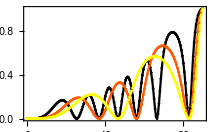

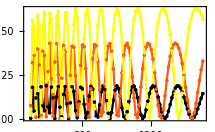

```mathematica
ang = Range[0,90,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 =  {1.5,1.5}  &/@ lda;

Chop[#*Conjugate[#]]&@Landau3MediaReflectionS[ang,{n1,n2,n3},lda,500*8];
Transpose@%//ListLinePlot[#,DataRange->{0,90}]&

ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 =  {1.5,1.5}  &/@ lda;

Chop[#*Conjugate[#]]&@Landau3MediaReflectionS[ang,{n1,n2,n3},lda,500*8];
%//ListLinePlot[#,DataRange->{500,1500}]&
```

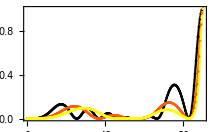

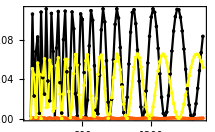

```mathematica
ang = Range[0,90,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = {1.5,1.5}  &/@ lda;

Chop[#*Conjugate[#]]&@Landau3MediaReflectionP[ang,{n1,n2,n3},lda,500*8];
Transpose@%//ListLinePlot[#,DataRange->{0,90}, PlotRange->All]&

ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 =  {1.5,1.5}  &/@ lda;

Chop[#*Conjugate[#]]&@Landau3MediaReflectionP[ang,{n1,n2,n3},lda,500*8];
%//ListLinePlot[#,DataRange->{500,1500}]&
```

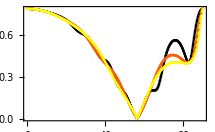
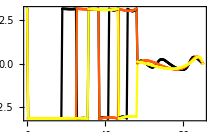

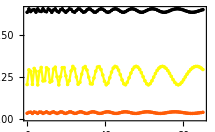
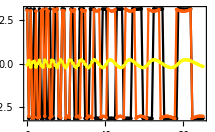

```mathematica
ang = Range[0,90,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = {1.5,1.5}  &/@ lda;

Landau3MediaElipsometry[ang,{n1,n2,n3},lda,500*8];
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]& /@ %

ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 =  {1.5,1.5}  &/@ lda;

Landau3MediaElipsometry[ang,{n1,n2,n3},lda,500*8];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ %
```

## Transfere Matrix

0.0202748

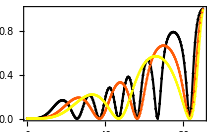

-Graphics-

```mathematica
TransferMatrixS[66*Pi/180.,{1,1.5,1},500.,500*8] [[1]];
Chop[#*Conjugate[#]]&@ %

ang = Range[0,90-.5,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;
TransferMatrixS[ang,{n1,n2,n3}, lda, 500*8] [[1]];
Chop[#*Conjugate[#]]&@%;
Transpose@%//ListLinePlot[#,DataRange->{0,90}]&


ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;
Chop[#*Conjugate[#]]&@TransferMatrixS[ang,{n1,n2,n3},lda,500*8][[1]];
%//ListLinePlot[#,DataRange->{500,1500}]&
```

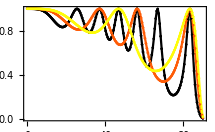

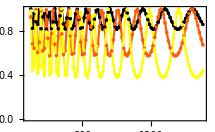

```mathematica
ang = Range[0,90-.5,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;

Through[{TransferMatrixImpedanceS, TransferMatrixS}[ang,{n1,n2,n3}, lda, 500*8] ];
#1*Chop[#2[[2]]*Conjugate[#2[[2]]]]&@@%;
Transpose@%//ListLinePlot[#,DataRange->{0,90}]&


ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;
Through[{TransferMatrixImpedanceS, TransferMatrixS}[ang,{n1,n2,n3}, lda, 500*8] ];
#1*Chop[#2[[2]]*Conjugate[#2[[2]]]]&@@%;
%//ListLinePlot[#,DataRange->{500,1500}]&
```

-0.00340336+0.0293503 ⅈ

0.000873024

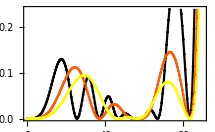

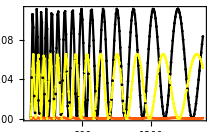

```mathematica
TransferMatrixP[66*Pi/180.,{1,{1.5,1.5},1},500.,500*8] [[1]]
Chop[#*Conjugate[#]]&@ %

ang = Range[0,90-.5,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;
TransferMatrixP[ang,{n1,n2,n3}, lda, 500*8] [[1]];
Chop[#*Conjugate[#]]&@%;
Transpose@%//ListLinePlot[#,DataRange->{0,90}]&


ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,5.];
n3 = n1 = 1 &/@lda;
n2 = {1.5,1.5}  &/@ lda;
Chop[#*Conjugate[#]]&@TransferMatrixP[ang,{n1,n2,n3},lda,500*8][[1]];
%//ListLinePlot[#,DataRange->{500,1500}]&
```

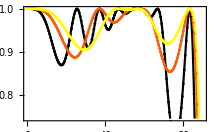

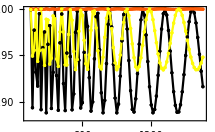

```mathematica
ang = Range[0,90-.5,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;

Through[{TransferMatrixImpedanceP, TransferMatrixP}[ang,{n1,n2,n3}, lda, 500*8] ];
#1*Chop[#2[[2]]*Conjugate[#2[[2]]]]&@@%;
Transpose@%//ListLinePlot[#,DataRange->{0,90}]&


ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;
Through[{TransferMatrixImpedanceP, TransferMatrixP}[ang,{n1,n2,n3}, lda, 500*8] ];
#1*Chop[#2[[2]]*Conjugate[#2[[2]]]]&@@%;
%//ListLinePlot[#,DataRange->{500,1500}]&
```

{0.204604,-0.0656263}

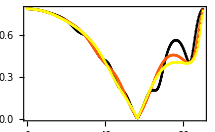
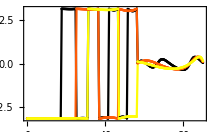

{-Graphics-,-Graphics-}

```mathematica
TransferMatrixElipsometry[66*Pi/180.,{1,1.5,1},500.,500*8]

ang = Range[.5,90-.5,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = {1.5,1.5}  &/@ lda;

TransferMatrixElipsometry[ang,{n1,n2,n3},lda,500*8];
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]& /@ %

ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 =  {1.5,1.5}  &/@ lda;

TransferMatrixElipsometry[ang,{n1,n2,n3},lda,500*8];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ %
```